# Natural gradient optimizer for linear problem

## Create ill-conditioned data

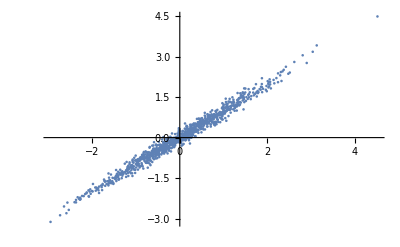

```mathematica
(* Random uniform vector normalized to 1 *)
randomD[f_]:=Module[{temp},
temp=RandomReal[{0,1},{f}];
temp/Total[temp]
];

(* centers data where batch dimension is 1 *)
centerData[X_]:=Module[{Xc},
Xc=Mean@Transpose@X;
Transpose[#-Xc&/@Transpose[X]]
];

dataSize[X_]:=Last@Dimensions@X
featureSize[X_]:=First@Dimensions@X

(* Generate data from 2D ill-posed distribution
e: controls how correlated variables are
yvar: variance of predicted variable
extraDims: add this many redundant variables equal to first
dsize: how many datapoints to sample
*)
generateXY[e_,yvar_,extraDims_,dsize_]:=Module[{wt,mean,cov,normal,pdf,X,Xc,Y,Xa,wta,w0a,XY,n,trueCov},
SeedRandom[0];
n=2;
wt={{1,1}}; (* true relation *)
mean=0&/@Range@n;
cov={{1, 1-e},{1-e,1}};
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
X=centerData[X];
Y=Dot[wt, X]+RandomVariate[NormalDistribution[0,√yvar]];
(* Add copies of first feature as redundant features *)
Xa= X~Join~Table[X[[1,All]],{i,extraDims}];
wta=Join[wt,{Table[0,{i,extraDims}]}, 2];
w0a=Join[{{1,2}},{Table[0,{i,extraDims}]}, 2];
{Xa,Y,w0a}
];
{X,Y,w0}=generateXY[0.01,1.,0,1000];
ListPlot[Transpose@X]
```

## Run Newton method

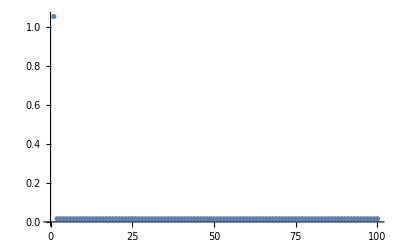

```mathematica
Clear[gradstep,err,weightedCov,pre,grad,loss];
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizeNewton[lr_,w0_,iters_]:=Module[{},
{pointList, gradList,preList, lossList}={{},{},{},{}};
Assert[Dimensions[w0]=={1,featureSize[X]}, "Incorrect w0"];
dsize=dataSize[X];
err[w_]:=Y-w.X;
grad[w_]:=-2err[w].Xᵀ/dsize;
loss[w_]:=take1@Flatten[err[w].err[w]ᵀ/dsize];

(* X weighted by error *)
Xw[w_]:=X.DiagonalMatrix@Flatten@err[w];

(* fisher = covariance weighted by error *)
pre[w_]:=PseudoInverse[X.Xᵀ/dsize];
w=w0;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~w;
gradList=gradList~Append~grad[w];
preList=preList~Append~pre[w];
lossList=lossList~Append~loss[w];
w=w-lr*grad[w].pre[w];
];
];

optimizeNewton[0.5, w0,100];
ListPlot@lossList
```

## Natural gradient

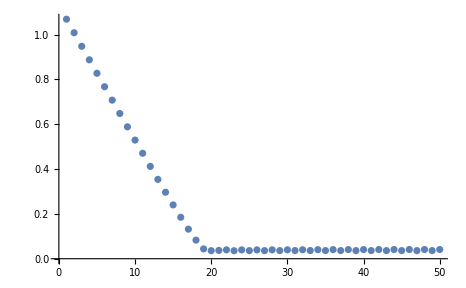

~/git/whitening/exp/data/natural_gradient_linear_data-1.csv

~/git/whitening/exp/data/natural_gradient_linear_losses-1.csv

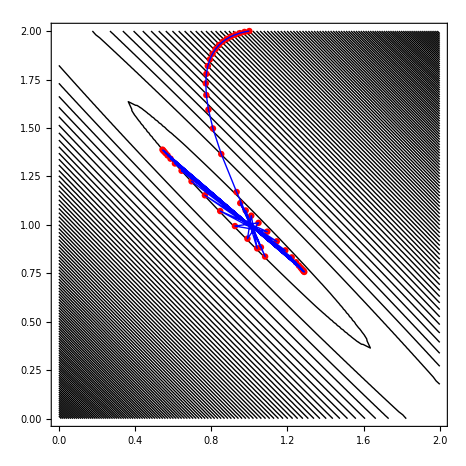

```mathematica
optimizeNatural[lr_,w0_,iters_]:=Module[{},
{pointList, gradList,preList, lossList,weightList}={{},{},{},{},{}};
Assert[Dimensions[w0]=={1,featureSize[X]}, "Incorrect w0"];
dsize=dataSize[X];
fsize=featureSize[X];
err[w_]:=Y-w.X;
(* To remove the effect of error decreasing, normalize average error *)
err2[w_]:=err[w]/Total[Abs[err[w]],2];
grad[w_]:=-2err[w].Xᵀ/dsize;
loss[w_]:=take1@Flatten[err[w].err[w]ᵀ/dsize];

weighting[w_]:=dsize Flatten[err[w]/Total[err[w]*err[w],2]];

(* the last one of these options takes effect *)
(* Newton's method *)
weighting[w_]:=Array[1&,{dsize}];

(* Random weighting, works like Newton's in practice *)
weighting[w_]:=Flatten@(dsize*randomD[dsize]);

(* Weigh by normalized error *) 
weighting[w_]:=dsize Flatten[err[w]/Total[Abs[err[w]],2]];

(* Weigh by unnormalized error *) 
weighting[w_]:=dsize Flatten[err[w]/Total[err[w],2]];

(* Weight by error aka natural gradient *) 
weighting[w_]:=Flatten[err[w]];
Xw[w_]:=X.DiagonalMatrix@(weighting[w]);


(* fisher = covariance weighted by error *)
fisher[w_]:=Xw[w].Xw[w]ᵀ/dsize;

pre[w_]:=PseudoInverse@fisher@w;
w=w0;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~w;
gradList=gradList~Append~grad[w];
preList=preList~Append~pre[w];
lossList=lossList~Append~loss[w];
weightList=weightList~Append~weighting[w];
w=w-lr*grad[w].pre[w];
];
];

{X,Y,w0}=generateXY[0.01,2,0,1000];
optimizeNatural[.05, w0,50];
ListPlot@lossList

bound=2;
plt1=ContourPlot[loss[{{x,y}}],{x,0,bound},{y,0,bound},Contours->100,ContourShading->None];
plotPoints=Flatten/@pointList[[;;50]];
plt3=Graphics[{Red,PointSize[0.01],Point[plotPoints]}];
plt4=Graphics[{Blue,Line[plotPoints]}];

Export["~/git/whitening/exp/data/natural_gradient_linear_data-1.csv",X~Join~Y]
Export["~/git/whitening/exp/data/natural_gradient_linear_losses-1.csv",lossList]

Show[{plt1,plt3,plt4}]
```

## Natural gradient with square root of Fisher

```mathematica
(* Symmetric square root *)
symsqrt[m_]:=Module[{U,S,W},
{U,S,W}=SingularValueDecomposition[m];
U.Sqrt[S].Transpose[W]
];
```

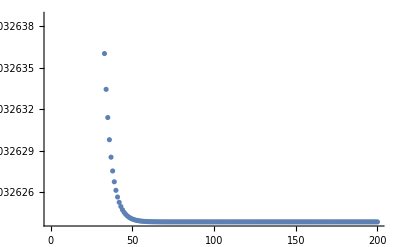

~/git/whitening/exp/data/natural_gradient_linear_data-1.csv

~/git/whitening/exp/data/natural_gradient_linear_losses-1.csv

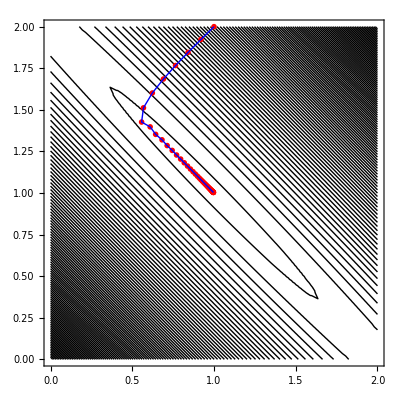

```mathematica
optimizeNaturalSqrt[lr_,w0_,iters_]:=Module[{},
{pointList, gradList,preList, lossList,weightList}={{},{},{},{},{}};
Assert[Dimensions[w0]=={1,featureSize[X]}, "Incorrect w0"];
dsize=dataSize[X];
fsize=featureSize[X];
err[w_]:=Y-w.X;
(* To remove the effect of error decreasing, normalize average error *)
err2[w_]:=err[w]/Total[Abs[err[w]],2];
grad[w_]:=-2err[w].Xᵀ/dsize;
loss[w_]:=take1@Flatten[err[w].err[w]ᵀ/dsize];

weighting[w_]:=dsize Flatten[err[w]/Total[err[w]*err[w],2]];

(* Newton's method *)
weighting[w_]:=Array[1&,{dsize}];

(* Random weighting *)
weighting[w_]:=Flatten@(dsize*randomD[dsize]);

(* Weigh by normalized error *) 
weighting[w_]:=dsize Flatten[err[w]/Total[Abs[err[w]],2]];

(* Weigh by unnormalized error *) 
weighting[w_]:=dsize Flatten[err[w]/Total[err[w],2]];

(* Weight by error aka natural gradient *) 
weighting[w_]:=Flatten[err[w]];
Xw[w_]:=X.DiagonalMatrix@(weighting[w]);


(* fisher = covariance weighted by error *)
fisher[w_]:=symsqrt[Xw[w].Xw[w]ᵀ/dsize];

pre[w_]:=PseudoInverse@fisher@w;
w=w0;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~w;
gradList=gradList~Append~grad[w];
preList=preList~Append~pre[w];
lossList=lossList~Append~loss[w];
weightList=weightList~Append~weighting[w];
w=w-lr*grad[w].pre[w];
];
];

{X,Y,w0}=generateXY[0.01,2,0,1000];
optimizeNaturalSqrt[.1, w0,200];
ListPlot@lossList

bound=2;
plt1=ContourPlot[loss[{{x,y}}],{x,0,bound},{y,0,bound},Contours->100,ContourShading->None];
plotPoints=Flatten/@pointList[[;;50]];
plt3=Graphics[{Red,PointSize[0.01],Point[plotPoints]}];
plt4=Graphics[{Blue,Line[plotPoints]}];

Export["~/git/whitening/exp/data/natural_gradient_linear_data-1.csv",X~Join~Y]
Export["~/git/whitening/exp/data/natural_gradient_linear_losses-1.csv",lossList]

Show[{plt1,plt3,plt4}]
```

## Linear expansion in Fisher direction

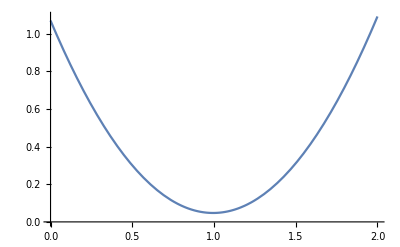

```mathematica
optimizeNatural[.05, w0,50];
plt1=Plot[loss[pointList[[1]]-x normalize[gradList[[1]].preList[[1]]]],{x,0,2}]
```

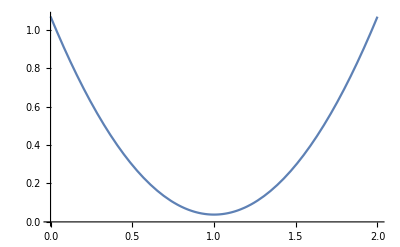

```mathematica
optimizeNaturalSqrt[.05, w0,50];
plt2=Plot[loss[pointList[[1]]-x normalize[ gradList[[1]].preList[[1]]]],{x,0,2}]
```

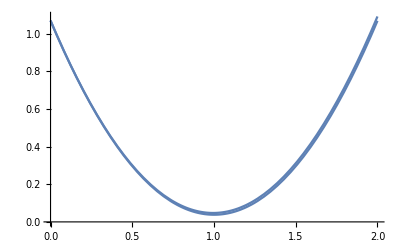

```mathematica
Show[{plt1,plt2}]
```